```mathematica
link2=Install["/Users/vicini/cernbox/codici/LoopTools-2.16/x86_64-Darwin/bin/LoopTools"];
SetMudim[91.1535^2];
```

====================================================
   FF 2.0, a package to evaluate one-loop integrals
 written by G. J. van Oldenborgh, NIKHEF-H, Amsterdam
 ====================================================
 for the algorithms used see preprint NIKHEF-H 89/17,
 'New Algorithms for One-loop Integrals', by G.J. van
 Oldenborgh and J.A.M. Vermaseren, published in 
 Zeitschrift fuer Physik C46(1990)425.
 ====================================================

```mathematica
(*
mymyB0i[q2_,m12_,m22_,mu2_] := Module[{ris,tmp},
qq2=q2;
nume=-NIntegrate[Log[(qq2 x^2-x(qq2+m12-m22)+m12-I 10^(-18))/mu2]   ,{x,0,1}];
ff=B0i[bb0,q2,m12,m22];

                               ris=Which[ qq2=!=0 && m12=!=0 && m22===m12, 
                                             ratio=-(qq2 + Sqrt[qq2*(-4*m12 + qq2)])/(qq2 - Sqrt[qq2*(-4*m12 + qq2)]);
                                             argratio=Arg[ratio];
                                             logratio=Log[Abs[ratio]];                                             
                                                         tmp=2 -Log[m12/mu2]- Sqrt[qq2*(-4*m12 + qq2)]*(logratio+I argratio)/qq2;

(*                                            Print[tmp/nume];
                                            Print[q2,"  ",m12,"  ",m22,"  ",tmp/nume,"  ",tmp/ff,"  ",nume];
                                            Print[argratio,"  ",Arg[qq2 + Sqrt[qq2*(-4*m12 + qq2)]]  ,"  ",Arg[  qq2 - Sqrt[qq2*(-4*m12 + qq2)]   ],"  ",Sqrt[qq2*(-4*m12 + qq2)]   ];*)

                                            tmp,
                                      qq2=!=0 && m12===qq2 && m22===0,
                                       tmp= 2 - Log[qq2/mu2];

                           tmp,
                                      qq2=!=0 && m22===qq2 && m12===0,
                                        2 - Log[qq2/mu2],
                                      qq2=!=0 && m12=!=0 && m22===0,
                                        tmp=2 - (1-m12/qq2)Log[m12-I 10^(-18)-qq2]-m12/qq2 Log[m12]+Log[mu2];
                           (*Print[tmp/nume];*)
                            tmp,
                                      qq2=!=0 && m12===0 && m22=!=0,
                                      tmp=2 - (1-m22/qq2)Log[m22-I 10^(-18)-qq2]-m22/qq2 Log[m22]+Log[mu2];
                           (*Print[tmp/nume];*)
                            tmp,
                                      qq2=!=0 && m12===0 && m22===0, 
                                        2 - Log[-qq2/mu2], 
                                      qq2===0 && m12=!=0 && m22===m12, 
                                          -Log[m12/mu2], 
                                      qq2===0 && m12===0 && m22===0, 
                                    0,
                       qq2===0 && m12=!=0 && m22===0, 
                                          1-Log[m12/mu2], 
                       qq2===0 && m22=!=0 && m12===0, 
                                          1-Log[m22/mu2], 
                                    qq2=!=0 && m12 =!= m22 && m12=!=0 && m22=!=0,
                          kallen=-4*(m22-I 10^(-18))*qq2 + (-m12 + m22 + qq2)^2;
                                     tmp=(4 - 2*Log[m12/(mu2)] + 
                                      ((-m12 + m22 + qq2 - Sqrt[kallen])*
                                      Log[(m12 - m22 + qq2 + Sqrt[kallen])/
                                              (m12 - m22 - qq2 + Sqrt[kallen])])/qq2 + 
                                      ((-m12 + m22 + qq2 + Sqrt[kallen])*
                                        Log[(-m12 + m22 - qq2 + Sqrt[kallen])/
                                                 (-m12 + m22 + qq2 + Sqrt[kallen])])/qq2)/2;
                           Print[tmp/nume];
                           tmp

                                    ];
         

                                                                        ris
                                    ];
*)

mymyB0i[q2_,m12_,m22_,mu2_] := Module[{ris,tmp},
qq2=q2;
nume=-NIntegrate[Log[(qq2 x^2-x(qq2+m12-m22)+m12-I 10^(-18))/mu2]   ,{x,0,1}];
(*ff=B0i[bb0,q2,m12,m22];*)

                               ris=Which[ qq2=!=0 && m12=!=0 && m22===m12, 
                                                 ratio=-(qq2 + Sqrt[qq2*(-4*m12 + qq2)])/(qq2 - Sqrt[qq2*(-4*m12 + qq2)]);
                                               argratio=Arg[ratio];
                                               logratio=Log[Abs[ratio]];                                             
                                               tmp=2 -Log[m12/mu2]- Sqrt[qq2*(-4*m12 + qq2)]*(logratio+I argratio)/qq2;
                                                tmp,

                                                 qq2=!=0 && m12===qq2 && m22===0,
                                                      tmp= 2 - Log[qq2/mu2];
                                                                      tmp,
                                                  qq2=!=0 && m22===qq2 && m12===0,
                                                        2 - Log[qq2/mu2],
                                                 qq2=!=0 && m12=!=0 && m22===0,
                                                       tmp=2 - (1-m12/qq2)Log[m12-I 10^(-18)-qq2]-m12/qq2 Log[m12]+Log[mu2];
                                                                      tmp,
                                                 qq2=!=0 && m12===0 && m22=!=0,
                                                         tmp=2 - (1-m22/qq2)Log[m22-I 10^(-18)-qq2]-m22/qq2 Log[m22]+Log[mu2];
                                                                      tmp,
                                                  qq2=!=0 && m12===0 && m22===0, 
                                                       2 - Log[-qq2/mu2], 
                                                  qq2===0 && m12=!=0 && m22===m12, 
                                                       -Log[m12/mu2], 
                                                  qq2===0 && m12===0 && m22===0, 
                                                              0,
                                                  qq2===0 && m12=!=0 && m22===0, 
                                                      1-Log[m12/mu2], 
                                                 qq2===0 && m22=!=0 && m12===0, 
                                                      1-Log[m22/mu2], 
                                               qq2===0 && m22=!=0 && m12=!=0, 
                                                    tmp= 1-(m12 Log[m12]-m22 Log[m22])/(m12-m22)+Log[mu2];
                                                   tmp, 
                                                  qq2=!=0 && m12 =!= m22 && m12=!=0 && m22=!=0,
                                                                         kallen=-4*(m22-I 10^(-18))*qq2 + (-m12 + m22 + qq2)^2;
                                                          tmp=(4 - 2*Log[m12/(mu2)] + 
                                                                     ((-m12 + m22 + qq2 - Sqrt[kallen])*
                                                                     Log[(m12 - m22 + qq2 + Sqrt[kallen])/
                                                                   (m12 - m22 - qq2 + Sqrt[kallen])])/qq2 + 
                                                                      ((-m12 + m22 + qq2 + Sqrt[kallen])*
                                                                     Log[(-m12 + m22 - qq2 + Sqrt[kallen])/
                                                                   (-m12 + m22 + qq2 + Sqrt[kallen])])/qq2)/2;
                                                                        tmp

                                    ];
         (*Print[qq2,"  ",m12,"  ",m22,"  ",ris];*)
(*Print[ris/nume];*)

                                                                        ris
                                    ];
```

```mathematica
$MinPrecision=32;
$MaxPrecision=32;
maindir = "/Users/vicini/cernbox/fisica/DY/DY-aas/narayan/DrellYan_QCDxEW/";
inputvalues=maindir<>"2L/grid-input-st.res";
Get[inputvalues];
fileborn=maindir<>"2L/formula-Born.res";
Get[fileborn];
filect=maindir<>"2L/Propagators/CT1L.m";
Get[filect];
```

```mathematica
subconst = {
	    ME->0.000511,
	    MM->0.105658,
	    ML->1.77682,
	    MUP->0.06983,
	    MD->0.06984,
	    MS->0.15,
	    MC->1.2,
	    MB->4.6,
	    MT->173.2,
	    ME2->ME^2,
	    MM2->MM^2,
	    ML2->ML^2,
	    MU2->MUP^2,
	    MD2->MD^2,
	    MS2->MS^2,
	    MC2->MC^2,
	    MB2->MB^2,
	    MT2->MT^2,
	    muW2->mW^2 - I GaW mW,
	    muZ2->mZ^2 - I GaZ mZ,
	    muWC2->mW^2 + I GaW mW,
	    muZC2->mZ^2 + I GaZ mZ,
	    muW->Sqrt[muW2],
	    muZ->Sqrt[muZ2],
	    mW->80.358,
	    mZ->91.1535,
	    GaW->2.084,
	    GaZ->2.4943 ,
	    MH2->125^2,
	    Alfa->1/137.035999074,
	    Alfas ->0.118};

subcharges = {
	      Ql->-1,
	      Qu->2/3,
	      Qd->-1/3,
	      I3l->-1/2,
	      I3u->1/2,
	      I3d->-1/2,
	      I3n->1/2,
	      NC->3};

subsymbols = {
	      gA4->gA^4,
	      gA->Sqrt[4 Pi Alfa],
	      aem->Alfa/4/Pi,
	      asr->Alfas/4/Pi,
	      Cf->(NC^2-1)/(2 NC),
	      borncf-> NC,
	      factml2L->factml1L^2,
	      mlflag->1,
	      IPi->I Pi,
	      gVu->1/2 I3u-Qu*sw2,
	      gAu->1/2 I3u,
	      gVd->1/2 I3d-Qd*sw2,
	      gAd->1/2 I3d,
	      gVl->1/2 I3l-Ql*sw2,
	      gAl->1/2 I3l,
	      gVn->1/2 I3n,
	      gAn->1/2 I3n,
	      gVuC->1/2 I3u-Qu*sw2C,
	      gAuC->1/2 I3u,
	      gVlC->1/2 I3l-Ql*sw2C,
	      gAlC->1/2 I3l,
	      gVuxx1->gVu^2 gVuC + gAu^2 gVuC + 2 gAu gAuC gVu,
	      gAuxx1->gAu^2 gAuC + gVu^2 gAuC + 2 gAu gVuC gVu,
	      gVlxx1->gVl^2 gVlC + gAl^2 gVlC + 2 gAl gAlC gVl,
	      gAlxx1->gAl^2 gAlC + gVl^2 gAlC + 2 gAl gVlC gVl,
	      gAlAuVlVu -> gAl gAu gVl,
	      gVl2PgAl2 -> gVl^2 gAl^2 ,
	      gVu2PgAu2 -> gVu^2 gAu^2,
	      gVlCPgAlC -> gVlC gAlC,
	      gVuCPgAuC -> gVuC gAuC,
	      ml->Sqrt[MM2],
	      ml2->MM2,
	      mZC2->muZC2,
	      mZ2->muZ2,
	      MZ2->muZ2,
	      MW2->muW2,
	      SW2->1-muW2/muZ2,
	      CW2->muW2/muZ2,
	      SW->Sqrt[SW2],
	      CW->Sqrt[CW2],
	      sw2->1-muW2/muZ2,
	      cw2->muW2/muZ2,
	      sw->Sqrt[sw2],
	      cw->Sqrt[1-sw2],
	      SW2C->1-muWC2/muZC2,
	      CW2C->muWC2/muZC2,
	      SWC->Sqrt[SW2C],
	      CWC->Sqrt[CW2C],
	      sw2C->1-muWC2/muZC2,
	      cw2C->muWC2/muZC2,
	      swC->Sqrt[sw2C],
	      cwC->Sqrt[1-sw2C],
	      S12->s12,
	      prc[x_,y_]->1/(x-y),
	      ratZoL2->muZ2/ml2,
	      ratZoW2->muZ2/muW2,
	      xsupx ->xZ/(1+xZ),
	      prop[S12,mZC2]->muZ2/(s12-muZC2),
	      cBpropmW->muW2/(s12-muZC2),
	      cBpropmZ->muZ2/(s12-muZC2),
	      conjBprop->1/(s12-muZC2),
	      cBpropml->ml2/(s12-muZC2),
	      c->1/2 + I Sqrt[3]/2,
	      cb->1/2-I Sqrt[3]/2,
	      G[0,m1]->I Pi,
	      z2->Zeta[2],
	      z3->1.20205690315959428539973768831929090417};
subkinvar={ vZ->zmz, vpZ -> zpmz, ypZ -> zZ, ypW->zW, vpW->zpmw,
       isqvpw->I Sqrt[zpmw], 
       isqvpz->I Sqrt[zpmz],
       isqvz->I Sqrt[zmz],
	   xl->-(Sqrt[s12]-Sqrt[-4*ml^2+s12])/(Sqrt[s12]+Sqrt[-4*ml^2+s12]),
	   yl->-s13/ml^2,
	   zl-> -s23/ml^2,
	   xW->-(Sqrt[s12]-Sqrt[-4*muW2+s12])/(Sqrt[s12]+Sqrt[-4*muW2+s12]),
	   yW->-s13/muW2, 
	   zW->-s23/muW2, 
	   xrW->-s12/muW2,
	   xZ-> -(Sqrt[s12]-Sqrt[-4*muZ2+s12])/(Sqrt[s12]+Sqrt[-4*muZ2+s12]),
	   yZ->-s13/muZ2,
	   zZ->-s23/muZ2,
	   xrZ->-s12/muZ2}; 

subflags={flagAA->1, flagAZ->1, flagZZ->1,flagW->1};
mur2=GetMudim[];
```

```mathematica
ZWF=deltagZminusDeltar1L //. subsymbols //. subconst/. myB0i[bb0,a_,b_,c_]:>mymyB0i[a,b,c,mur2];

gamma2[s12_] = (s12-muZ2 + selfZZ[s12]- selfZZ[muZ2]) //. subsymbols //.subconst /.myB0i[bb0,a_,b_,c_]:>mymyB0i[a,b,c,mur2];

full[s12_] = ((1+ZWF)/(s12-muZ2 + selfZZ[s12]- selfZZ[muZ2]) )//. subsymbols //.subconst /. myB0i[bb0,a_,b_,c_]:>mymyB0i[a,b,c,mur2];

g1[s12_] = (selfZZ[s12]- selfZZ[muZ2] -(s12-muZ2) ZWF     )/(s12-muZ2)  //. subsymbols //.subconst /. myB0i[bb0,a_,b_,c_]:>mymyB0i[a,b,c,mur2];

oneloop[s12_] = 1/(s12-muZ2) (1-  g1[s12]    ) //. subsymbols //.subconst /. myB0i[bb0,a_,b_,c_]:>mymyB0i[a,b,c,mur2];

tree[s12_] = 1/(s12-muZ2)//.subconst ;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99949703120001495639142252702669111386057920753955841064453125}. NIntegrate obtained -2.25594+3.11403 ⅈ and 6.28111×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.000280851}. NIntegrate obtained -2.2539+3.11491 ⅈ and 0.0000294145 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99949703120001495639142252702669111386057920753955841064453125}. NIntegrate obtained -2.25594+3.11403 ⅈ and 6.28111×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.000280851}. NIntegrate obtained -2.00294+3.11307 ⅈ and 0.0000263775 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99949703120001495639142252702669111386057920753955841064453125}. NIntegrate obtained -2.00631+3.11169 ⅈ and 0.0000476045 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0031055}. NIntegrate obtained -2.03475+3.09737 ⅈ and 0.0000555693 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::inumr: The integrand Log[0.000120352 (-ⅈ/1000000000000000000-s12 x+s12 x^2)] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand Log[0.000120352 ((2.61121×10^-7-1.×10^-18 ⅈ)-(0.+s12) x+s12 x^2)] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.000280851}. NIntegrate obtained -2.00294+3.11307 ⅈ and 0.0000263775 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99949703120001495639142252702669111386057920753955841064453125}. NIntegrate obtained -2.00631+3.11169 ⅈ and 0.0000476045 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0031055}. NIntegrate obtained -2.03475+3.09737 ⅈ and 0.0000555693 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::inumr: The integrand Log[0.000120352 (-ⅈ/1000000000000000000-s12 x+s12 x^2)] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand Log[0.000120352 ((2.61121×10^-7-1.×10^-18 ⅈ)-(0.+s12) x+s12 x^2)] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.000280851}. NIntegrate obtained -2.00294+3.11307 ⅈ and 0.0000263775 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.99949703120001495639142252702669111386057920753955841064453125}. NIntegrate obtained -2.00631+3.11169 ⅈ and 0.0000476045 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0031055}. NIntegrate obtained -2.03475+3.09737 ⅈ and 0.0000555693 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::inumr: The integrand Log[0.000120352 (-ⅈ/1000000000000000000-s12 x+s12 x^2)] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand Log[0.000120352 ((2.61121×10^-7-1.×10^-18 ⅈ)-(0.+s12) x+s12 x^2)] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

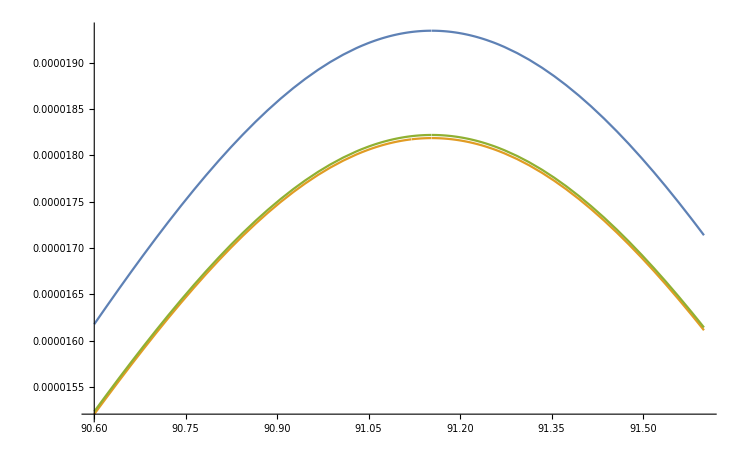

```mathematica
Plot[ {Evaluate[Re[1/(en^2-muZC2) tree[en^2]//.subconst]],
         Evaluate[Re[1/(en^2-muZC2) full[en^2]//.subconst]],
         Evaluate[Re[1/(en^2-muZC2) oneloop[en^2]//.subconst]]   },{en,90.6,91.6}]
```

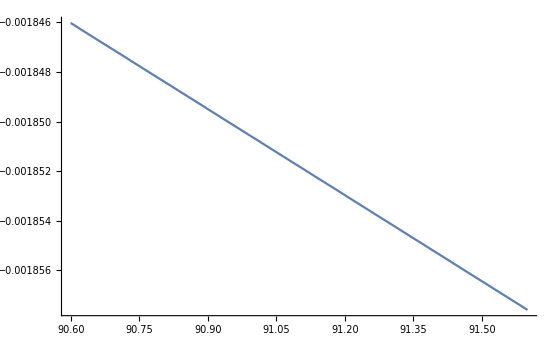

```mathematica
Plot[  Evaluate[Re[ 1/(en^2-muZC2) full[en^2]]/Re[oneloop[en^2]/(en^2-muZC2)]//.subconst]-1,{en,90.6,91.6}, PlotRange->All]
```

```mathematica
selfZZ[muZ2] //. subsymbols //. subconst /. myB0i :> B0i /.myB0i[bb0,a_,b_,c_]:>mymyB0i[a,b,c,mur2]/; Head[a]===Complex /. myB0i :> B0i
```

Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented

235.688+212.358 ⅈ

```mathematica
B0i[bb0,6450,0,0.0048776256]
```

2.25327+3.14159 ⅈ

```mathematica
mymyB0i[6450-0.00001I,0,0.0048776256,mur2]
```

2.25327-3.14159 ⅈ

```mathematica
ch[qq2_,m12_]=(qq2 - Sqrt[qq2*(-4*m12 + qq2)])/(qq2 + Sqrt[qq2*(-4*m12 + qq2)])
```

((6450.-0.00001 ⅈ)-√((6450.-0.00001 ⅈ) ((6450.-0.00001 ⅈ)-4 m12)))/((6450.-0.00001 ⅈ)+√((6450.-0.00001 ⅈ) ((6450.-0.00001 ⅈ)-4 m12)))

```mathematica
ch[8300-I 0.000001,0.05]
```

7.75206×10^-6+1.20189×10^-14 ⅈ

```mathematica
GetMudim[]
```

8308.96

```mathematica
c[a1_,a2_,a3_] := Re[mymyB0i[a1,a2,a3,mur2]/B0i[bb0,a1,a2,a3]]
```

Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented
 Complex momenta not implemented

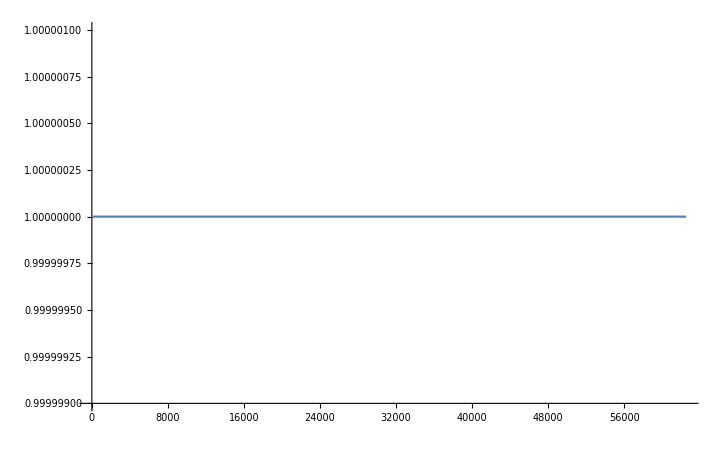

```mathematica
Plot[ c[s-I 250,125^2,91^2-I  250], {s,10^2,250^2},PlotRange->{0.999999,1.000001}]
```

```mathematica
165^2
```

27225

```mathematica
Pexact[p2_] = I (1+dZ0)/(p2-mu2 + G[p2]-G[mu2])
```

(ⅈ (1+dZ0))/(-mu2+p2-G[mu2]+G[p2])

```mathematica
Poneloop[p2_] = I/(p2-mu2) + I/(p2-mu2)(G[mu2]-G[p2]+(p2-mu2) dZ0)/(p2-mu2)// Simplify
```

-(ⅈ ((1+dZ0) (mu2-p2)-G[mu2]+G[p2]))/(mu2-p2)^2

```mathematica
(Pexact[a]-Poneloop[a])  // Together // Simplify
```

(ⅈ (G[a]-G[mu2]) (dZ0 (-a+mu2)+G[a]-G[mu2]))/((a-mu2)^2 (a-mu2+G[a]-G[mu2]))

```mathematica
Normal[ Series[ %12, {eps,0,0}]]
```

-1/(144 π SW2)Alfa (-4 muW2 (11+2 CW2+2 SW2)+3 (-24 MB2-36 MD2-8 ME2+3 MH2-8 ML2-8 MM2-24 MS2+12 MT2+12 MU2+28 MW2+MZ2+8 CW2 MZ2-16 MW2 SW2+2 (6 MC2+6 MD2+2 ME2-MH2+2 ML2+2 MM2+6 MS2+6 MT2+6 MU2-14 MW2+4 CW2 MW2-MZ2-8 CW2 MZ2+4 MW2 SW2))+1/muW2 3 (6 MB2^2+6 MC2^2+6 MD2^2+2 ME2^2-MH2^2+2 ML2^2+2 MM2^2-12 MC2 MS2+6 MS2^2-12 MB2 MT2+6 MT2^2-12 MD2 MU2+6 MU2^2+2 MH2 MW2-2 MW2^2-8 CW2 MW2^2+2 MW2 MZ2+16 CW2 MW2 MZ2-MZ2^2-8 CW2 MZ2^2-8 MW2^2 SW2+muW2 (24 MB2-12 MC2+24 MD2+4 ME2-MH2+4 ML2+4 MM2+12 MS2-24 MT2-24 MU2-8 CW2 MW2+MZ2+8 CW2 MZ2+8 MW2 SW2)))+1/(144 π SW2)Alfa (-4 s12 (11+2 CW2+2 SW2)+3 (-24 MB2-36 MD2-8 ME2+3 MH2-8 ML2-8 MM2-24 MS2+12 MT2+12 MU2+28 MW2+MZ2+8 CW2 MZ2-16 MW2 SW2+2 (6 MC2+6 MD2+2 ME2-MH2+2 ML2+2 MM2+6 MS2+6 MT2+6 MU2-14 MW2+4 CW2 MW2-MZ2-8 CW2 MZ2+4 MW2 SW2))+1/s12 3 (6 MB2^2+6 MC2^2+6 MD2^2+2 ME2^2-MH2^2+2 ML2^2+2 MM2^2-12 MC2 MS2+6 MS2^2-12 MB2 MT2+6 MT2^2-12 MD2 MU2+6 MU2^2+2 MH2 MW2-2 MW2^2-8 CW2 MW2^2+2 MW2 MZ2+16 CW2 MW2 MZ2-MZ2^2-8 CW2 MZ2^2-8 MW2^2 SW2+s12 (24 MB2-12 MC2+24 MD2+4 ME2-MH2+4 ML2+4 MM2+12 MS2-24 MT2-24 MU2-8 CW2 MW2+MZ2+8 CW2 MZ2+8 MW2 SW2)))-(Alfa MB2 (-6+(MB2-MT2+4 muW2)/muW2) myB0i[bb0,0,MB2,MB2])/(8 π SW2)+(Alfa MB2 (-6+(MB2-MT2+4 s12)/s12) myB0i[bb0,0,MB2,MB2])/(8 π SW2)-(Alfa MC2 (MC2-MS2-2 muW2) myB0i[bb0,0,MC2,MC2])/(8 muW2 π SW2)+(Alfa MC2 (MC2-MS2-2 s12) myB0i[bb0,0,MC2,MC2])/(8 π s12 SW2)-(Alfa MD2 (-6+(MD2-MU2+4 muW2)/muW2) myB0i[bb0,0,MD2,MD2])/(8 π SW2)+(Alfa MD2 (-6+(MD2-MU2+4 s12)/s12) myB0i[bb0,0,MD2,MD2])/(8 π SW2)-(Alfa ME2 (-4+(ME2+2 muW2)/muW2) myB0i[bb0,0,ME2,ME2])/(24 π SW2)+(Alfa ME2 (-4+(ME2+2 s12)/s12) myB0i[bb0,0,ME2,ME2])/(24 π SW2)+(Alfa MH2 (-3+(MH2+muW2-MW2)/muW2) myB0i[bb0,0,MH2,MH2])/(48 π SW2)-(Alfa MH2 (-3+(MH2-MW2+s12)/s12) myB0i[bb0,0,MH2,MH2])/(48 π SW2)-(Alfa ML2 (-4+(ML2+2 muW2)/muW2) myB0i[bb0,0,ML2,ML2])/(24 π SW2)+(Alfa ML2 (-4+(ML2+2 s12)/s12) myB0i[bb0,0,ML2,ML2])/(24 π SW2)-(Alfa MM2 (-4+(MM2+2 muW2)/muW2) myB0i[bb0,0,MM2,MM2])/(24 π SW2)+(Alfa MM2 (-4+(MM2+2 s12)/s12) myB0i[bb0,0,MM2,MM2])/(24 π SW2)-(Alfa MS2 (-4+(-MC2+MS2+2 muW2)/muW2) myB0i[bb0,0,MS2,MS2])/(8 π SW2)+(Alfa MS2 (-4+(-MC2+MS2+2 s12)/s12) myB0i[bb0,0,MS2,MS2])/(8 π SW2)-(Alfa MT2 (2+(-MB2+MT2-4 muW2)/muW2) myB0i[bb0,0,MT2,MT2])/(8 π SW2)+(Alfa MT2 (2+(-MB2+MT2-4 s12)/s12) myB0i[bb0,0,MT2,MT2])/(8 π SW2)-(Alfa MU2 (2+(-MD2+MU2-4 muW2)/muW2) myB0i[bb0,0,MU2,MU2])/(8 π SW2)+(Alfa MU2 (2+(-MD2+MU2-4 s12)/s12) myB0i[bb0,0,MU2,MU2])/(8 π SW2)+(Alfa MW2 (4 (-7+4 SW2)-(MH2-2 MW2-8 CW2 MW2+MZ2+8 CW2 MZ2-8 muW2 (CW2-SW2)-8 MW2 SW2)/muW2) myB0i[bb0,0,MW2,MW2])/(48 π SW2)-(Alfa MW2 (4 (-7+4 SW2)-(MH2-2 MW2-8 CW2 MW2+MZ2+8 CW2 MZ2-8 s12 (CW2-SW2)-8 MW2 SW2)/s12) myB0i[bb0,0,MW2,MW2])/(48 π SW2)-(Alfa (1+8 CW2) (1+(muW2+MW2-MZ2)/muW2) MZ2 myB0i[bb0,0,MZ2,MZ2])/(48 π SW2)+(Alfa (1+8 CW2) MZ2 (1+(MW2-MZ2+s12)/s12) myB0i[bb0,0,MZ2,MZ2])/(48 π SW2)+(Alfa (-1+ME2/muW2) (ME2+2 muW2) myB0i[bb0,muW2,0,ME2])/(24 π SW2)+(Alfa (-1+ML2/muW2) (ML2+2 muW2) myB0i[bb0,muW2,0,ML2])/(24 π SW2)+(Alfa (-1+MM2/muW2) (MM2+2 muW2) myB0i[bb0,muW2,0,MM2])/(24 π SW2)-(Alfa (-11 muW2+5 MW2+(MW2 (-muW2+MW2))/muW2) myB0i[bb0,muW2,0,MW2])/(6 π)+(Alfa (-3 MB2+5 MT2-2 muW2+((MB2-MT2) (MB2-MT2+4 muW2))/muW2) myB0i[bb0,muW2,MB2,MT2])/(8 π SW2)+(Alfa (3 MC2-MS2+((MC2-MS2) (MC2-MS2-2 muW2))/muW2-2 muW2) myB0i[bb0,muW2,MC2,MS2])/(8 π SW2)+(Alfa (-3 MD2+5 MU2-2 muW2+((MD2-MU2) (MD2-MU2+4 muW2))/muW2) myB0i[bb0,muW2,MD2,MU2])/(8 π SW2)-(Alfa (-3 MH2+muW2+((MH2-MW2) (MH2+muW2-MW2))/muW2+11 MW2) myB0i[bb0,muW2,MH2,MW2])/(48 π SW2)-(Alfa ((CW2-88 CW2^2) muW2+9 CW2 MW2-12 CW2^2 MW2+(CW2 (1+8 CW2) (MW2-MZ2) (muW2+MW2-MZ2))/muW2-CW2 MZ2-8 CW2^2 MZ2-24 CW2 MW2 SW2+12 MW2 SW2^2) myB0i[bb0,muW2,MW2,MZ2])/(48 CW2 π SW2)+flagWW1L (-muW+s12) ((-0.0569889-0.00250438 ⅈ)-1/muW2(-1/(48 π SW2)Alfa (-24 MB2-36 MD2-8 ME2+3 MH2-8 ML2-8 MM2-24 MS2+12 MT2+12 MU2+28 MW2+MZ2+8 CW2 MZ2-16 MW2 SW2+2 (6 MC2+6 MD2+2 ME2-MH2+2 ML2+2 MM2+6 MS2+6 MT2+6 MU2-14 MW2+4 CW2 MW2-MZ2-8 CW2 MZ2+4 MW2 SW2))+1/(144 π SW2)Alfa (-4 muW2 (11+2 CW2+2 SW2)+3 (-24 MB2-36 MD2-8 ME2+3 MH2-8 ML2-8 MM2-24 MS2+12 MT2+12 MU2+28 MW2+MZ2+8 CW2 MZ2-16 MW2 SW2+2 (6 MC2+6 MD2+2 ME2-MH2+2 ML2+2 MM2+6 MS2+6 MT2+6 MU2-14 MW2+4 CW2 MW2-MZ2-8 CW2 MZ2+4 MW2 SW2))+1/muW2 3 (6 MB2^2+6 MC2^2+6 MD2^2+2 ME2^2-MH2^2+2 ML2^2+2 MM2^2-12 MC2 MS2+6 MS2^2-12 MB2 MT2+6 MT2^2-12 MD2 MU2+6 MU2^2+2 MH2 MW2-2 MW2^2-8 CW2 MW2^2+2 MW2 MZ2+16 CW2 MW2 MZ2-MZ2^2-8 CW2 MZ2^2-8 MW2^2 SW2+muW2 (24 MB2-12 MC2+24 MD2+4 ME2-MH2+4 ML2+4 MM2+12 MS2-24 MT2-24 MU2-8 CW2 MW2+MZ2+8 CW2 MZ2+8 MW2 SW2)))-(Alfa ME2 myB0i[bb0,0,0,ME2])/(24 π SW2)-(Alfa ML2 myB0i[bb0,0,0,ML2])/(24 π SW2)-(Alfa MM2 myB0i[bb0,0,0,MM2])/(24 π SW2)-(5 Alfa MW2 myB0i[bb0,0,0,MW2])/(6 π)+(3 Alfa MB2 myB0i[bb0,0,MB2,MB2])/(4 π SW2)+(Alfa MB2 (-6+(MB2-MT2+4 muW2)/muW2) myB0i[bb0,0,MB2,MB2])/(8 π SW2)+(Alfa (-3 MB2+5 MT2) myB0i[bb0,0,MB2,MT2])/(8 π SW2)+(Alfa MC2 (MC2-MS2-2 muW2) myB0i[bb0,0,MC2,MC2])/(8 muW2 π SW2)+(Alfa (3 MC2-MS2) myB0i[bb0,0,MC2,MS2])/(8 π SW2)+(3 Alfa MD2 myB0i[bb0,0,MD2,MD2])/(4 π SW2)+(Alfa MD2 (-6+(MD2-MU2+4 muW2)/muW2) myB0i[bb0,0,MD2,MD2])/(8 π SW2)+(Alfa (-3 MD2+5 MU2) myB0i[bb0,0,MD2,MU2])/(8 π SW2)+(Alfa ME2 myB0i[bb0,0,ME2,ME2])/(6 π SW2)+(Alfa ME2 (-4+(ME2+2 muW2)/muW2) myB0i[bb0,0,ME2,ME2])/(24 π SW2)-(Alfa MH2 myB0i[bb0,0,MH2,MH2])/(16 π SW2)-(Alfa MH2 (-3+(MH2+muW2-MW2)/muW2) myB0i[bb0,0,MH2,MH2])/(48 π SW2)-(Alfa (-3 MH2+11 MW2) myB0i[bb0,0,MH2,MW2])/(48 π SW2)+(Alfa ML2 myB0i[bb0,0,ML2,ML2])/(6 π SW2)+(Alfa ML2 (-4+(ML2+2 muW2)/muW2) myB0i[bb0,0,ML2,ML2])/(24 π SW2)+(Alfa MM2 myB0i[bb0,0,MM2,MM2])/(6 π SW2)+(Alfa MM2 (-4+(MM2+2 muW2)/muW2) myB0i[bb0,0,MM2,MM2])/(24 π SW2)+(Alfa MS2 myB0i[bb0,0,MS2,MS2])/(2 π SW2)+(Alfa MS2 (-4+(-MC2+MS2+2 muW2)/muW2) myB0i[bb0,0,MS2,MS2])/(8 π SW2)-(Alfa MT2 myB0i[bb0,0,MT2,MT2])/(4 π SW2)+(Alfa MT2 (2+(-MB2+MT2-4 muW2)/muW2) myB0i[bb0,0,MT2,MT2])/(8 π SW2)-(Alfa MU2 myB0i[bb0,0,MU2,MU2])/(4 π SW2)+(Alfa MU2 (2+(-MD2+MU2-4 muW2)/muW2) myB0i[bb0,0,MU2,MU2])/(8 π SW2)+(Alfa MW2 (-7+4 SW2) myB0i[bb0,0,MW2,MW2])/(12 π SW2)-(Alfa MW2 (4 (-7+4 SW2)-(MH2-2 MW2-8 CW2 MW2+MZ2+8 CW2 MZ2-8 muW2 (CW2-SW2)-8 MW2 SW2)/muW2) myB0i[bb0,0,MW2,MW2])/(48 π SW2)-(Alfa (9 CW2 MW2-12 CW2^2 MW2-CW2 MZ2-8 CW2^2 MZ2-24 CW2 MW2 SW2+12 MW2 SW2^2) myB0i[bb0,0,MW2,MZ2])/(48 CW2 π SW2)-(Alfa (1+8 CW2) MZ2 myB0i[bb0,0,MZ2,MZ2])/(48 π SW2)+(Alfa (1+8 CW2) (1+(muW2+MW2-MZ2)/muW2) MZ2 myB0i[bb0,0,MZ2,MZ2])/(48 π SW2)-(Alfa (-1+ME2/muW2) (ME2+2 muW2) myB0i[bb0,muW2,0,ME2])/(24 π SW2)-(Alfa (-1+ML2/muW2) (ML2+2 muW2) myB0i[bb0,muW2,0,ML2])/(24 π SW2)-(Alfa (-1+MM2/muW2) (MM2+2 muW2) myB0i[bb0,muW2,0,MM2])/(24 π SW2)+(Alfa (-11 muW2+5 MW2+(MW2 (-muW2+MW2))/muW2) myB0i[bb0,muW2,0,MW2])/(6 π)-(Alfa (-3 MB2+5 MT2-2 muW2+((MB2-MT2) (MB2-MT2+4 muW2))/muW2) myB0i[bb0,muW2,MB2,MT2])/(8 π SW2)-(Alfa (3 MC2-MS2+((MC2-MS2) (MC2-MS2-2 muW2))/muW2-2 muW2) myB0i[bb0,muW2,MC2,MS2])/(8 π SW2)-(Alfa (-3 MD2+5 MU2-2 muW2+((MD2-MU2) (MD2-MU2+4 muW2))/muW2) myB0i[bb0,muW2,MD2,MU2])/(8 π SW2)+(Alfa (-3 MH2+muW2+((MH2-MW2) (MH2+muW2-MW2))/muW2+11 MW2) myB0i[bb0,muW2,MH2,MW2])/(48 π SW2)+(Alfa ((CW2-88 CW2^2) muW2+9 CW2 MW2-12 CW2^2 MW2+(CW2 (1+8 CW2) (MW2-MZ2) (muW2+MW2-MZ2))/muW2-CW2 MZ2-8 CW2^2 MZ2-24 CW2 MW2 SW2+12 MW2 SW2^2) myB0i[bb0,muW2,MW2,MZ2])/(48 CW2 π SW2)))-(Alfa (-1+ME2/s12) (ME2+2 s12) myB0i[bb0,s12,0,ME2])/(24 π SW2)-(Alfa (-1+ML2/s12) (ML2+2 s12) myB0i[bb0,s12,0,ML2])/(24 π SW2)-(Alfa (-1+MM2/s12) (MM2+2 s12) myB0i[bb0,s12,0,MM2])/(24 π SW2)+(Alfa (5 MW2+(MW2 (MW2-s12))/s12-11 s12) myB0i[bb0,s12,0,MW2])/(6 π)-(Alfa (-3 MB2+5 MT2-2 s12+((MB2-MT2) (MB2-MT2+4 s12))/s12) myB0i[bb0,s12,MB2,MT2])/(8 π SW2)-(Alfa (3 MC2-MS2+((MC2-MS2) (MC2-MS2-2 s12))/s12-2 s12) myB0i[bb0,s12,MC2,MS2])/(8 π SW2)-(Alfa (-3 MD2+5 MU2-2 s12+((MD2-MU2) (MD2-MU2+4 s12))/s12) myB0i[bb0,s12,MD2,MU2])/(8 π SW2)+(Alfa (-3 MH2+11 MW2+s12+((MH2-MW2) (MH2-MW2+s12))/s12) myB0i[bb0,s12,MH2,MW2])/(48 π SW2)+(Alfa (9 CW2 MW2-12 CW2^2 MW2-CW2 MZ2-8 CW2^2 MZ2+(CW2-88 CW2^2) s12+(CW2 (1+8 CW2) (MW2-MZ2) (MW2-MZ2+s12))/s12-24 CW2 MW2 SW2+12 MW2 SW2^2) myB0i[bb0,s12,MW2,MZ2])/(48 CW2 π SW2)